## OLD

```mathematica
α[max_,w_,x_,τ_,θ_]:=max*Exp[-(x-θ)^2/(2 τ^2)];
p1[x_,μ1_,sig_]:=1/(√(2π sig^2))Exp[-(x-μ1)^2/(2 sig^2)];
p2[x_,μ2_,sig_]:=1/(√(2π sig^2))Exp[-(x-μ2)^2/(2 sig^2)];
```

```mathematica
Manipulate[Plot[NIntegrate[α[2,w,x,τ,θ]*(w *p1[x,μ1,1]+(1-w)*p2[x,μ2,1]),{x,-∞,∞}],{w,0,1}, PlotRange->{0,4}],{{θ,2},0,10},{{μ1,2},0,10},{{μ2,2},0,10},{{τ,2},0,10}]
```

```mathematica
(1-w)=N1/(N1+s N2);w=(s N2)/(N1+s N2)
leaving w = s
```

```mathematica
Manipulate[sol=NDSolve[{N1'[t]==N1[t]/(N1[t]+s N2[t])*(max τ)/(√(τ^2+sig^2))*Exp[-(x1[t]-θ1)^2/(2(τ^2+sig^2))]N1[t]+(s N2[t])/(N1[t]+s N2[t])*(max τ)/(√(τ^2+sig^2))*Exp[-(x2[t]-θ1)^2/(2(τ^2+sig^2))]s N2[t]-(m+s)N1[t],
N2'[t]==N2[t]/(s N1[t]+N2[t])*(max τ)/(√(τ^2+sig^2))*Exp[-(x2[t]-θ2)^2/(2(τ^2+sig^2))]N2[t]+(s N1[t])/(s N1[t]+N2[t])*(max τ)/(√(τ^2+sig^2))*Exp[-(x1[t]-θ2)^2/(2(τ^2+sig^2))]s N1[t]-(m+s) N1[t],
x1'[t]==-Var(ⅇ^(-(x1[t]-θ1)^2/(2 (sig^2+τ^2))) max (x1[t]-θ1) τ N1[t])/((sig^2+τ^2)^(3/2) (N1[t]+s N2[t])),
x2'[t]==-Var(ⅇ^(-(x2[t]-θ2)^2/(2 (sig^2+τ^2))) max (x2[t]-θ2) τ N2[t])/((sig^2+τ^2)^(3/2) (s N1[t]+N2[t])), N1[0]==2,N2[0]==2,x1[0]==8,x2[0]==10},{N1[t],N2[t],x1[t],x2[t]},{t,0,200}];
densities=Plot[Evaluate[{N1[t],N2[t]}/.sol],{t,0,100},PlotRange->{0,50}];
traits=Plot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,100}, PlotRange->{0,20}];
GraphicsGrid[{{densities,traits}}],
{{max,0.046},0,2},{{τ,1},0.001,3},{{sig,1},0.001,3},{{θ1,5},0,20},{{θ2,10},0,20},{{m,0.001},0,4},{{Var,1},0,2},{{s,0.0001},0,0.1}
]
```

```mathematica
D[(N1[t]/(N1[t]+s N2[t])*(max τ)/(√(τ^2+sig^2))*Exp[-(x1-θ1)^2/(2(τ^2+sig^2))]),x1]
```

-(ⅇ^(-(x1-θ1)^2/(2 (sig^2+τ^2))) max (x1-θ1) τ N1[t])/((sig^2+τ^2)^(3/2) (N1[t]+s N2[t]))

## Discrete time (base model)

### Ricker model

```mathematica
Clear[Tmax,z,rmax,β,θ1,θ2,τ,m,σ]
```

```mathematica
(* Parameters *)
Tmax=200; (* Number of generations simulated *)
z= 0.5;(* within-generation death rate *)
rmax=2; (* maximal per-capita growth rate *)
m=0.5; (* straying rate *)
β = 0.1; (* density dependence *)
θ1=10; (* Environmental optimum in site 1 *)
θ2=2; (* Environmental optimum in site 2 *)
τ=1; (* Strength of selection: the smaller the number, the larger selection *)
σ=1; (* Standard deviation of starting populations *)
(* Initialize variables *)
N1=Array[0&,Tmax+1];
N2=Array[0&,Tmax+1];
x1=Array[0&,Tmax+1];
x2=Array[0&,Tmax+1];
N1[[1]]=2;N2[[1]]=2;x1[[1]]=2;x2[[1]]=2;
(* Selection function *)
α[rmax_,x_,τ_,θ_]:=rmax*Exp[-(x-θ)^2/(2 τ^2)];
(* Trait distributions *)
p1[x_,μ1_,σ_]=PDF[NormalDistribution[μ1,σ],x];
p2[x_,μ2_,σ_]=PDF[NormalDistribution[μ2,σ],x];

(* Average fitness W of individuals with traits x *)
(* Integrate[α[rmax,x,τ,θ]*(w p1[x,μ1,1]+(1-w)p2[x,μ2,1]),{x,-∞,∞}], then take derivatives with respect to μ1 and μ2 to get *)
meanFit1=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1];
meanFit2=D[Log[w(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2];

(* Calculate reproductive rates: outside of loop and init for speed *)
(*r1Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r1Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
r1Site1=(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site1=(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2));r1Site2=(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site2=(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));
```

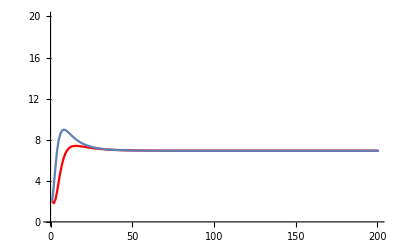

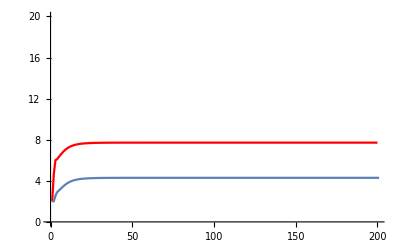

```mathematica
(* Simulation loop *)
Table[
(* Calculate reprod using mixture distribution after migration *)
r1Site1EQ=r1Site1*N1[[i]]/(N1[[i]]+m N2[[i]])/.{μ1->x1[[i]]};r2Site1EQ=r2Site1*(m N2[[i]])/(N1[[i]]+m N2[[i]])/.{μ2->x2[[i]]};r1Site2EQ=r1Site2*(m N1[[i]])/(m N1[[i]]+N2[[i]])/.{μ1->x1[[i]]};r2Site2EQ=r2Site2*N2[[i]]/(m N1[[i]]+N2[[i]])/.{μ2->x2[[i]]};
(* Find biomass at time t+1 *)
N1[[i+1]]=(N1[[i]]+m N2[[i]])ⅇ^-z+(r1Site1EQ N1[[i]]+r2Site1EQ m N2[[i]])ⅇ^(-β(N1[[i]]+m N2[[i]]));
N2[[i+1]]=(N2[[i]]+m N1[[i]])ⅇ^-z+(r2Site2EQ N2[[i]]+r1Site2EQ m N1[[i]])ⅇ^(-β(N2[[i]]+m N1[[i]]));
(* Find mean trait value at time t+1 *)
x1[[i+1]]=(w x1[[i]]+(1-w)x2[[i]]+meanFit1)/.{θ->θ1,μ1->x1[[i]],μ2->x2[[i]],w->N1[[i]]/(N1[[i]]+m N2[[i]])};
x2[[i+1]]=(w x2[[i]]+(1-w)x1[[i]]+meanFit2)/.{θ->θ2,μ1->x1[[i]],μ2->x2[[i]],w->N2[[i]]/(m N1[[i]]+N2[[i]])};
,{i,1,Tmax}];
toplotN1=Table[{i,N1[[i]]},{i,1,Tmax}];
toplotN2=Table[{i,N2[[i]]},{i,1,Tmax}];
toplotx1=Table[{i,x1[[i]]},{i,1,Tmax}];
toplotx2=Table[{i,x2[[i]]},{i,1,Tmax}];
Show[ListPlot[toplotN1,PlotStyle->Red, PlotRange->{0,20}, Joined->True],ListPlot[N2, Joined->True, PlotRange->All]]
Show[ListPlot[toplotx1,PlotStyle->Red,PlotRange->{0,20}, Joined->True],ListPlot[x2, Joined->True, PlotRange->All]]
```

## Model function

```mathematica
ClearAll["Global`*"]
```

```mathematica
Clear[Tmax,z,rmax,β,θ1,θ2,τ,m,σ]
```

```mathematica
EvolvingKevin[Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_]:=Block[{},
(* Initialize variables *)
N1=Array[0&,Tmax+1];
N2=Array[0&,Tmax+1];
x1=Array[0&,Tmax+1];
x2=Array[0&,Tmax+1];
N1[[1]]=2;N2[[1]]=2;x1[[1]]=initμ1;x2[[1]]=initμ2;
(* Trait distributions *)
p1[x_,μ1_]=PDF[NormalDistribution[μ1,σ],x];
p2[x_,μ2_]=PDF[NormalDistribution[μ2,σ],x];

(* Average fitness W of individuals with traits x *)
(* Integrate[α[rmax,x,τ,θ]*(w p1[x,μ1,1]+(1-w)p2[x,μ2,1]),{x,-∞,∞}], then take derivatives with respect to μ1 and μ2 to get *)
meanFit1=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1];
meanFit2=D[Log[w(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2];

(* Calculate reproductive rates: outside of loop and init for speed *)
(*r1Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r1Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
r1Site1=(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site1=(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2));r1Site2=(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site2=(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));
(* Simulation loop *)
Table[
(* Calculate reprod using mixture distribution after migration *)
r1Site1EQ=r1Site1*N1[[i]]/(N1[[i]]+m N2[[i]])/.{μ1->x1[[i]]};r2Site1EQ=r2Site1*(m N2[[i]])/(N1[[i]]+m N2[[i]])/.{μ2->x2[[i]]};r1Site2EQ=r1Site2*(m N1[[i]])/(m N1[[i]]+N2[[i]])/.{μ1->x1[[i]]};r2Site2EQ=r2Site2*N2[[i]]/(m N1[[i]]+N2[[i]])/.{μ2->x2[[i]]};
(* Find biomass at time t+1 *)
(* It now takes into account the fact that a fraction of the population leaves the site as -m N1[[i]] *)
N1[[i+1]]=((1-m)N1[[i]]+m N2[[i]])ⅇ^-z+(r1Site1EQ N1[[i]]+r2Site1EQ m N2[[i]]-m N1[[i]])ⅇ^(-β((1-m)N1[[i]]+m N2[[i]])); 
N2[[i+1]]=((1-m)N2[[i]]+m N1[[i]])ⅇ^-z+(r2Site2EQ N2[[i]]+r1Site2EQ m N1[[i]]-m N2[[i]])ⅇ^(-β((1-m)N2[[i]]+m N1[[i]]));
(* Find mean trait value at time t+1 *)
x1[[i+1]]=(w x1[[i]]+(1-w)x2[[i]]+meanFit1)/.{θ->θ1,μ1->x1[[i]],μ2->x2[[i]],w->N1[[i]]/(N1[[i]]+m N2[[i]])};
x2[[i+1]]=(w x2[[i]]+(1-w)x1[[i]]+meanFit2)/.{θ->θ2,μ1->x1[[i]],μ2->x2[[i]],w->N2[[i]]/(m N1[[i]]+N2[[i]])};
,{i,1,Tmax}];
toplotN1=Table[{i,N1[[i]]},{i,1,Tmax}];
toplotN2=Table[{i,N2[[i]]},{i,1,Tmax}];
toplotx1=Table[{i,x1[[i]]},{i,1,Tmax}];
toplotx2=Table[{i,x2[[i]]},{i,1,Tmax}];

]
```

```mathematica
EvolvingKevinStochastic[Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_,processerror_]:=Block[{},
(* Initialize variables *)
N1=Array[0&,Tmax+1];
N2=Array[0&,Tmax+1];
x1=Array[0&,Tmax+1];
x2=Array[0&,Tmax+1];
N1[[1]]=2;N2[[1]]=2;x1[[1]]=initμ1;x2[[1]]=initμ2;
(* Trait distributions *)
p1[x_,μ1_]=PDF[NormalDistribution[μ1,σ],x];
p2[x_,μ2_]=PDF[NormalDistribution[μ2,σ],x];

(* Average fitness W of individuals with traits x *)
(* Integrate[α[rmax,x,τ,θ]*(w p1[x,μ1,1]+(1-w)p2[x,μ2,1]),{x,-∞,∞}], then take derivatives with respect to μ1 and μ2 to get *)
meanFit1=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1];
meanFit2=D[Log[w(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2];

(* Calculate reproductive rates: outside of loop and init for speed *)
(*r1Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r1Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
r1Site1=(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site1=(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2));r1Site2=(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site2=(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));
(* Simulation loop *)
Table[
(* Calculate reprod using mixture distribution after migration *)
r1Site1EQ=r1Site1*N1[[i]]/(N1[[i]]+m N2[[i]])/.{μ1->x1[[i]]};r2Site1EQ=r2Site1*(m N2[[i]])/(N1[[i]]+m N2[[i]])/.{μ2->x2[[i]]};r1Site2EQ=r1Site2*(m N1[[i]])/(m N1[[i]]+N2[[i]])/.{μ1->x1[[i]]};r2Site2EQ=r2Site2*N2[[i]]/(m N1[[i]]+N2[[i]])/.{μ2->x2[[i]]};
(* Find biomass at time t+1 *)
(* It now takes into account the fact that a fraction of the population leaves the site as -m N1[[i]] *)
N1[[i+1]]=((1-m)N1[[i]]+m N2[[i]])ⅇ^-z+((r1Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])* N1[[i]]+(r2Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])* m N2[[i]]-m N1[[i]])ⅇ^(-β((1-m)N1[[i]]+m N2[[i]])); 
N2[[i+1]]=((1-m)N2[[i]]+m N1[[i]])ⅇ^-z+((r2Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* N2[[i]]+(r1Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* m N1[[i]]-m N2[[i]])ⅇ^(-β((1-m)N2[[i]]+m N1[[i]]));
(* Find mean trait value at time t+1 *)
x1[[i+1]]=(w x1[[i]]+(1-w)x2[[i]]+meanFit1)/.{θ->θ1,μ1->x1[[i]],μ2->x2[[i]],w->N1[[i]]/(N1[[i]]+m N2[[i]])};
x2[[i+1]]=(w x2[[i]]+(1-w)x1[[i]]+meanFit2)/.{θ->θ2,μ1->x1[[i]],μ2->x2[[i]],w->N2[[i]]/(m N1[[i]]+N2[[i]])};
,{i,1,Tmax}];
toplotN1=Table[{i,N1[[i]]},{i,1,Tmax}];
toplotN2=Table[{i,N2[[i]]},{i,1,Tmax}];
toplotx1=Table[{i,x1[[i]]},{i,1,Tmax}];
toplotx2=Table[{i,x2[[i]]},{i,1,Tmax}];

]
```

```mathematica
(* N1, N2, X1, X2 against m *)
(*Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_*)
Reps=50;
mig=Array[0.+0.02 # &,Reps];
MinN1=Array[0.  # &,Reps];MaxN1=Array[0.  # &,Reps];MeanN1=Array[0.  # &,Reps];
MinN2=Array[0.  # &,Reps];MaxN2=Array[0.  # &,Reps];MeanN2=Array[0.  # &,Reps];
PE=Array[0.  # &,Reps];
Minx1=Array[0.  # &,Reps];Maxx1=Array[0.  # &,Reps];Meanx1=Array[0.  # &,Reps];
Minx2=Array[0.  # &,Reps];Maxx2=Array[0.  # &,Reps];Meanx2=Array[0.  # &,Reps];
Table[EvolvingKevinStochastic[
(*Tmax*)200,
(*z*)0.5,
(*rmax*)2,
(*β*)0.1,
(*θ1*)10,
(*θ2*)5,
(*initμ1*)10,
(*initμ2*)5,
(*τ*)1,
(*σ*)1,
(*m*)mig[[i]],
(*processerror*)0.1];
MinN1[[i]]=Min[N1];MaxN1[[i]]=Max[N1];MeanN1[[i]]=Mean[N1[[100;;200]]];
MinN2[[i]]=Min[N2];MaxN2[[i]]=Max[N2];MeanN2[[i]]=Mean[N2[[100;;200]]];
PE[[i]] = (Mean[{StandardDeviation[N1[[100;;200]]],StandardDeviation[N2[[100;;200]]]}]/ Mean[{Mean[N1[[100;;200]]],Mean[N2[[100;;200]]]}])*(1/(StandardDeviation[N1[[100;;200]]+N2[[100;;200]]]/Mean[N1[[100;;200]]+N2[[100;;200]]]));
Minx1[[i]]=Min[x1];Maxx1[[i]]=Max[x1];Meanx1[[i]]=Mean[x1[[100;;200]]];
Minx2[[i]]=Min[N2];Maxx2[[i]]=Max[x2];Meanx2[[i]]=Mean[x2[[100;;200]]];
,{i,1,Reps}];
toplotN1=Table[{mig[[i]],MeanN1[[i]]},{i,1,Reps}];
toplotN2=Table[{mig[[i]],MeanN2[[i]]},{i,1,Reps}];
toplotx1=Table[{mig[[i]],10-Meanx1[[i]]},{i,1,Reps}];
toplotx2=Table[{mig[[i]],5-Meanx2[[i]]},{i,1,Reps}];
toplotPE=Table[{mig[[i]],PE[[i]]},{i,1,Reps}];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

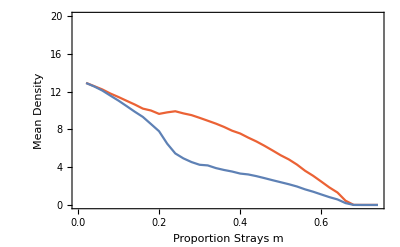

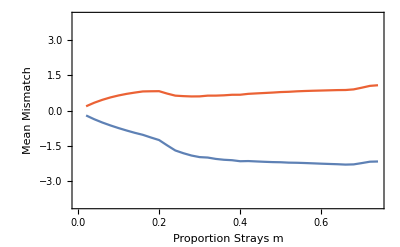

```mathematica
(* Mean density against m *)
Show[
ListPlot[toplotN1,PlotStyle->ColorData[97,4], PlotRange->{0,20}, Joined->True,Frame->True,FrameLabel->{"Proportion Strays m","Mean Density"}],
ListPlot[toplotN2, Joined->True, PlotRange->All]
]
(* Mean mismatch against m *)
Show[
ListPlot[toplotx1,PlotStyle->ColorData[97,4], PlotRange->{-4,4}, Joined->True,Frame->True,FrameLabel->{"Proportion Strays m","Mean Mismatch"}],
ListPlot[toplotx2, Joined->True, PlotRange->All]
]
```

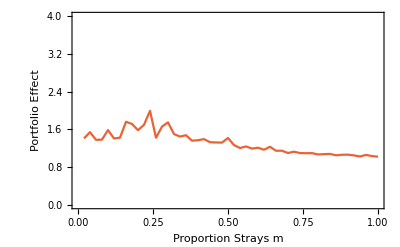

```mathematica
(* Mean mismatch against m *)
Show[
ListPlot[toplotPE,PlotStyle->ColorData[97,4], PlotRange->{0,4}, Joined->True,Frame->True,FrameLabel->{"Proportion Strays m","Portfolio Effect"},PlotRange->All]
]
```

### Individual Trajectory

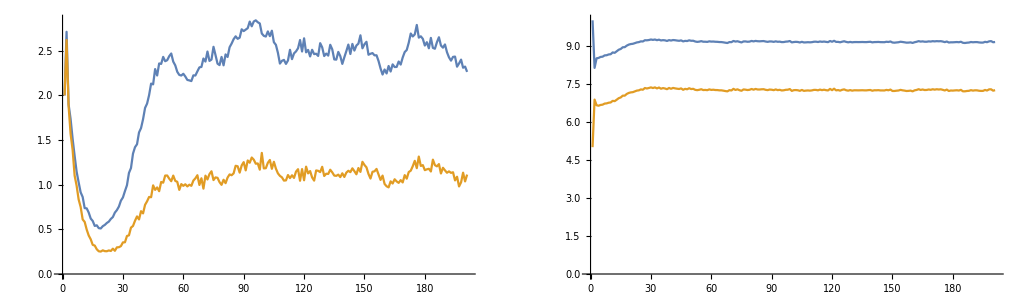

```mathematica
out=EvolvingKevinStochastic[
(*Tmax*)200,
(*z*)0.5,
(*rmax*)2,
(*β*)0.1,
(*θ1*)10,
(*θ2*)5,
(*initμ1*)10,
(*initμ2*)5,
(*τ*)1,
(*σ*)1,
(*m*)0.6,
(*processerror*)0.1
]
GraphicsGrid[{{
ListPlot[{N1,N2},Joined->True,PlotRange->{0,All}],
ListPlot[{x1,x2},Joined->True]
}}]
```

```mathematica
PE
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,47.3994,511.621,239.631,68.5078,3.70481,32.9038,1.78377,1.05013,1.09301,1.02873,1.00521,1.05776,1.18172,1.10145,1.0181,1.01388,1.01252,1.02091,1.16928,1.00814,1.09769,1.00656,1.00336,1.02925,1.0005,1.00017,1.,1.,1.,1.,1.,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}